Approximaatio m_(kevein sneutriino) == M_(sneutriinot)_(4,4) ja g1 = g2 = Yn_ij = 0.

```mathematica
f=MN33^2-2 lambda lambdaN v1 v2+2 AlambdaN lambdaN vevS+2 kappa lambdaN vevS^2+4 lambdaN^2 vevS^2;
g=f/.{lambda->0.2,kappa->0.1,v1->174*Cos@ArcTan@5,v2->174*Sin@ArcTan@5,MN33->MNR,vevS->130./0.2}
```

82171.1 lambdaN+1300. AlambdaN lambdaN+1.69×10^6 lambdaN^2+MNR^2

```mathematica
mass[lambdaN_,AlambdaN_,MNR_]:=Sqrt@(82171.07692307692 lambdaN+1300. AlambdaN lambdaN+1.69*^6 lambdaN^2+MNR^2)
```

Tässä plotissa pinta on paikka jossa m_(kevein sneutriino) = 25.  Uudemman Cerdenon Fig3:ssa skannataan lambda_N ja A_lambda_N [0.1,0.8] ja [-1000,-200] vastaavasti. Vaatimus että m_(kevein sneutriino) < 25 GeV vastaa sitten noin tuota pintaa MNR:n funktiona.

```mathematica
RegionPlot3D[Re@mass[x,y,z]<25,{x,0.1,0.8},{y,-200,-1000},{z,0,500}]
```

-Graphics3D-

Tässä on scatter plotti jonka micromegas tuottaa. (peilikuva yllä olevasta plotista koska en osaa laittaa akseleta kuriin). MNR oli rajoitettu < 400 minkä vuoksi kartiosta on pieni pala leikkautunt pois.

-Graphics3D-

Tässä sama plotti mutta rajoitus relic density =~ 0.15. Nätisti näkyy kuinka leikaa tuosta kartiosta pari aluetta sallittuja pisteitä.

Projektio lambda_N, A_lambda_N tasolle jonka pitäisi olla nyt sama kuin Cerdeno Fig 3 (right).

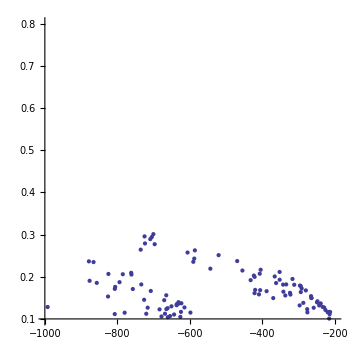
```mathematica
-Graphics--Graphics-
```

Jokseenkin oikein se ylempi alue, mutta alempi alue puuttuu Cerdenolta. Emme ole vielä tarkistaneet rikkooko tuon alueen pisteet jotain muuta rajoitusta vastaan (esim liian kevyt neutralino tms).